Harmonic Oscillator w/ quartic term

H = -d^2/dx^2 + X^2 + k X^4

```mathematica
x[i_, j_]:=1/(√2)√i KroneckerDelta[j, i-1] + 1/(√2)√(i+1)KroneckerDelta[j, i+1]
```

```mathematica
basisSize=50;
xRep = Array[x, {basisSize, basisSize},0];
xSquared =MatrixPower[Array[x, {basisSize, basisSize},0], 2];
xQuart =MatrixPower[Array[x, {basisSize, basisSize},0], 4];
```

```mathematica
dx[i_, j_]:=(−1/(√2)√i KroneckerDelta[j, i-1] + 1/(√2)√(i+1)KroneckerDelta[j, i+1])
```

```mathematica
dxRep = Array[dx, {basisSize, basisSize},0];
dxSquared =MatrixPower[Array[dx, {basisSize, basisSize},0], 2];
```

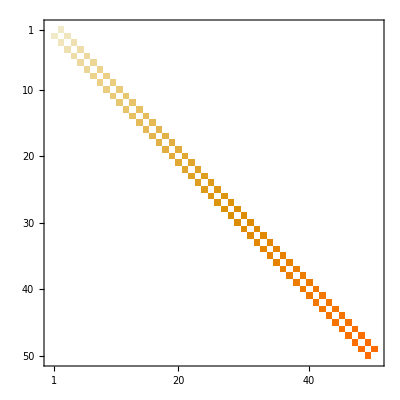

\left(
\begin{array}{cccccccccc}
 0 & \frac{1}{\sqrt{2}} & 0 & 0 & 0 & 0 & 0 & 0 & 0 & 0 \\
 \frac{1}{\sqrt{2}} & 0 & 1 & 0 & 0 & 0 & 0 & 0 & 0 & 0 \\
 0 & 1 & 0 & \sqrt{\frac{3}{2}} & 0 & 0 & 0 & 0 & 0 & 0 \\
 0 & 0 & \sqrt{\frac{3}{2}} & 0 & \sqrt{2} & 0 & 0 & 0 & 0 & 0 \\
 0 & 0 & 0 & \sqrt{2} & 0 & \sqrt{\frac{5}{2}} & 0 & 0 & 0 & 0 \\
 0 & 0 & 0 & 0 & \sqrt{\frac{5}{2}} & 0 & \sqrt{3} & 0 & 0 & 0 \\
 0 & 0 & 0 & 0 & 0 & \sqrt{3} & 0 & \sqrt{\frac{7}{2}} & 0 & 0 \\
 0 & 0 & 0 & 0 & 0 & 0 & \sqrt{\frac{7}{2}} & 0 & 2 & 0 \\
 0 & 0 & 0 & 0 & 0 & 0 & 0 & 2 & 0 & \frac{3}{\sqrt{2}} \\
 0 & 0 & 0 & 0 & 0 & 0 & 0 & 0 & \frac{3}{\sqrt{2}} & 0 \\
\end{array}
\right)

```mathematica
xRep //MatrixPlot
xRep[[1;;10,1;;10]] //MatrixForm  //TeXForm
```

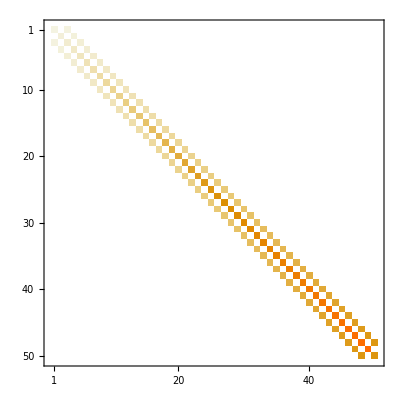

\left(
\begin{array}{cccccccccc}
 \frac{1}{2} & 0 & \frac{1}{\sqrt{2}} & 0 & 0 & 0 & 0 & 0 & 0 & 0 \\
 0 & \frac{3}{2} & 0 & \sqrt{\frac{3}{2}} & 0 & 0 & 0 & 0 & 0 & 0 \\
 \frac{1}{\sqrt{2}} & 0 & \frac{5}{2} & 0 & \sqrt{3} & 0 & 0 & 0 & 0 & 0 \\
 0 & \sqrt{\frac{3}{2}} & 0 & \frac{7}{2} & 0 & \sqrt{5} & 0 & 0 & 0 & 0 \\
 0 & 0 & \sqrt{3} & 0 & \frac{9}{2} & 0 & \sqrt{\frac{15}{2}} & 0 & 0 & 0 \\
 0 & 0 & 0 & \sqrt{5} & 0 & \frac{11}{2} & 0 & \sqrt{\frac{21}{2}} & 0 & 0 \\
 0 & 0 & 0 & 0 & \sqrt{\frac{15}{2}} & 0 & \frac{13}{2} & 0 & \sqrt{14} & 0 \\
 0 & 0 & 0 & 0 & 0 & \sqrt{\frac{21}{2}} & 0 & \frac{15}{2} & 0 & 3 \sqrt{2} \\
 0 & 0 & 0 & 0 & 0 & 0 & \sqrt{14} & 0 & \frac{17}{2} & 0 \\
 0 & 0 & 0 & 0 & 0 & 0 & 0 & 3 \sqrt{2} & 0 & \frac{19}{2} \\
\end{array}
\right)

```mathematica
xSquared//MatrixPlot
xSquared[[1;;10,1;;10]] //MatrixForm //TeXForm
```

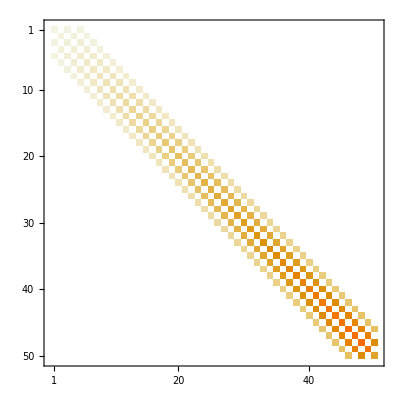

\left(
\begin{array}{cccccccccc}
 \frac{3}{4} & 0 & \frac{3}{\sqrt{2}} & 0 & \sqrt{\frac{3}{2}} & 0 & 0 & 0 & 0 & 0 \\
 0 & \frac{15}{4} & 0 & 5 \sqrt{\frac{3}{2}} & 0 & \sqrt{\frac{15}{2}} & 0 & 0 & 0 & 0 \\
 \frac{3}{\sqrt{2}} & 0 & \frac{39}{4} & 0 & 7 \sqrt{3} & 0 & 3 \sqrt{\frac{5}{2}} & 0 & 0 & 0 \\
 0 & 5 \sqrt{\frac{3}{2}} & 0 & \frac{75}{4} & 0 & 9 \sqrt{5} & 0 & \sqrt{\frac{105}{2}} & 0 & 0 \\
 \sqrt{\frac{3}{2}} & 0 & 7 \sqrt{3} & 0 & \frac{123}{4} & 0 & 11 \sqrt{\frac{15}{2}} & 0 & \sqrt{105} & 0 \\
 0 & \sqrt{\frac{15}{2}} & 0 & 9 \sqrt{5} & 0 & \frac{183}{4} & 0 & 13 \sqrt{\frac{21}{2}} & 0 & 3 \sqrt{21} \\
 0 & 0 & 3 \sqrt{\frac{5}{2}} & 0 & 11 \sqrt{\frac{15}{2}} & 0 & \frac{255}{4} & 0 & 15 \sqrt{14} & 0 \\
 0 & 0 & 0 & \sqrt{\frac{105}{2}} & 0 & 13 \sqrt{\frac{21}{2}} & 0 & \frac{339}{4} & 0 & 51 \sqrt{2} \\
 0 & 0 & 0 & 0 & \sqrt{105} & 0 & 15 \sqrt{14} & 0 & \frac{435}{4} & 0 \\
 0 & 0 & 0 & 0 & 0 & 3 \sqrt{21} & 0 & 51 \sqrt{2} & 0 & \frac{543}{4} \\
\end{array}
\right)

```mathematica
xQuart//MatrixPlot
xQuart[[1;;10,1;;10]] // MatrixForm//TeXForm
```

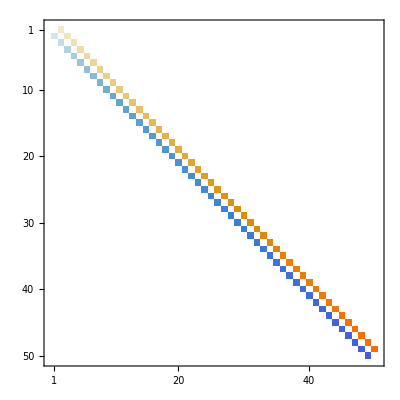

\left(
\begin{array}{cccccccccc}
 0 & \frac{1}{\sqrt{2}} & 0 & 0 & 0 & 0 & 0 & 0 & 0 & 0 \\
 -\frac{1}{\sqrt{2}} & 0 & 1 & 0 & 0 & 0 & 0 & 0 & 0 & 0 \\
 0 & -1 & 0 & \sqrt{\frac{3}{2}} & 0 & 0 & 0 & 0 & 0 & 0 \\
 0 & 0 & -\sqrt{\frac{3}{2}} & 0 & \sqrt{2} & 0 & 0 & 0 & 0 & 0 \\
 0 & 0 & 0 & -\sqrt{2} & 0 & \sqrt{\frac{5}{2}} & 0 & 0 & 0 & 0 \\
 0 & 0 & 0 & 0 & -\sqrt{\frac{5}{2}} & 0 & \sqrt{3} & 0 & 0 & 0 \\
 0 & 0 & 0 & 0 & 0 & -\sqrt{3} & 0 & \sqrt{\frac{7}{2}} & 0 & 0 \\
 0 & 0 & 0 & 0 & 0 & 0 & -\sqrt{\frac{7}{2}} & 0 & 2 & 0 \\
 0 & 0 & 0 & 0 & 0 & 0 & 0 & -2 & 0 & \frac{3}{\sqrt{2}} \\
 0 & 0 & 0 & 0 & 0 & 0 & 0 & 0 & -\frac{3}{\sqrt{2}} & 0 \\
\end{array}
\right)

```mathematica
dxRep //MatrixPlot
dxRep[[1;;10,1;;10]] //MatrixForm //TeXForm
```

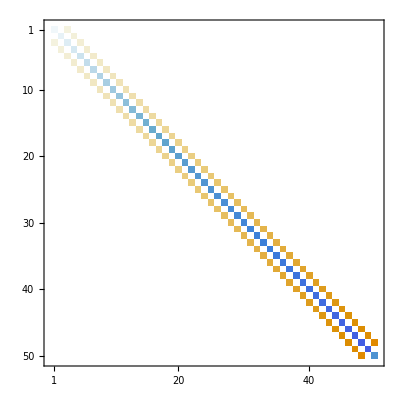

\left(
\begin{array}{cccccccccc}
 -\frac{1}{2} & 0 & \frac{1}{\sqrt{2}} & 0 & 0 & 0 & 0 & 0 & 0 & 0 \\
 0 & -\frac{3}{2} & 0 & \sqrt{\frac{3}{2}} & 0 & 0 & 0 & 0 & 0 & 0 \\
 \frac{1}{\sqrt{2}} & 0 & -\frac{5}{2} & 0 & \sqrt{3} & 0 & 0 & 0 & 0 & 0 \\
 0 & \sqrt{\frac{3}{2}} & 0 & -\frac{7}{2} & 0 & \sqrt{5} & 0 & 0 & 0 & 0 \\
 0 & 0 & \sqrt{3} & 0 & -\frac{9}{2} & 0 & \sqrt{\frac{15}{2}} & 0 & 0 & 0 \\
 0 & 0 & 0 & \sqrt{5} & 0 & -\frac{11}{2} & 0 & \sqrt{\frac{21}{2}} & 0 & 0 \\
 0 & 0 & 0 & 0 & \sqrt{\frac{15}{2}} & 0 & -\frac{13}{2} & 0 & \sqrt{14} & 0 \\
 0 & 0 & 0 & 0 & 0 & \sqrt{\frac{21}{2}} & 0 & -\frac{15}{2} & 0 & 3 \sqrt{2} \\
 0 & 0 & 0 & 0 & 0 & 0 & \sqrt{14} & 0 & -\frac{17}{2} & 0 \\
 0 & 0 & 0 & 0 & 0 & 0 & 0 & 3 \sqrt{2} & 0 & -\frac{19}{2} \\
\end{array}
\right)

```mathematica
dxSquared //MatrixPlot
dxSquared[[1;;10,1;;10]] //MatrixForm  //TeXForm
```

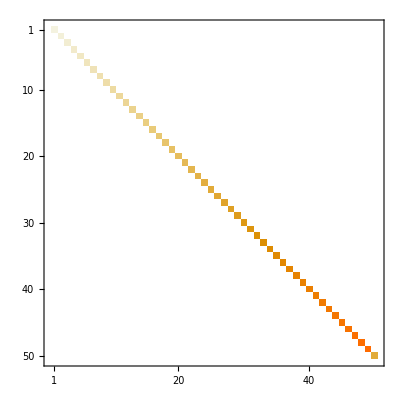

```mathematica
-dxSquared + xSquared//MatrixPlot
```

⟨m| H |n⟩ = ⟨m| E_n |n⟩ = E_n δ_nm

```mathematica
1/2(-dxSquared + xSquared)[[1;;10,1;;10]]//MatrixForm //TeXForm
```

\left(
\begin{array}{cccccccccc}
 \frac{1}{2} & 0 & 0 & 0 & 0 & 0 & 0 & 0 & 0 & 0 \\
 0 & \frac{3}{2} & 0 & 0 & 0 & 0 & 0 & 0 & 0 & 0 \\
 0 & 0 & \frac{5}{2} & 0 & 0 & 0 & 0 & 0 & 0 & 0 \\
 0 & 0 & 0 & \frac{7}{2} & 0 & 0 & 0 & 0 & 0 & 0 \\
 0 & 0 & 0 & 0 & \frac{9}{2} & 0 & 0 & 0 & 0 & 0 \\
 0 & 0 & 0 & 0 & 0 & \frac{11}{2} & 0 & 0 & 0 & 0 \\
 0 & 0 & 0 & 0 & 0 & 0 & \frac{13}{2} & 0 & 0 & 0 \\
 0 & 0 & 0 & 0 & 0 & 0 & 0 & \frac{15}{2} & 0 & 0 \\
 0 & 0 & 0 & 0 & 0 & 0 & 0 & 0 & \frac{17}{2} & 0 \\
 0 & 0 & 0 & 0 & 0 & 0 & 0 & 0 & 0 & \frac{19}{2} \\
\end{array}
\right)

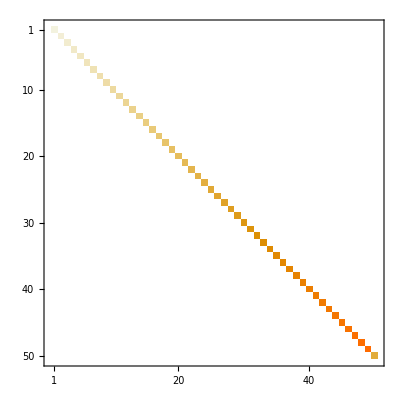

```mathematica
HoH=1/2(-dxSquared + xSquared);
HoH//MatrixPlot
```

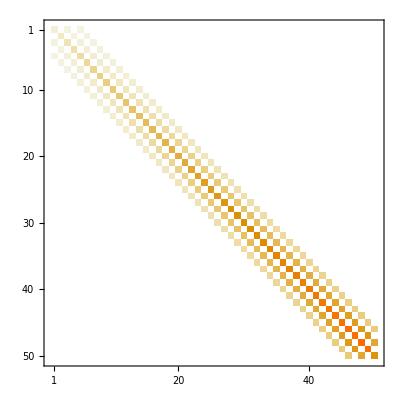

(103/200 | 0 | 3/(50 √2) | 0 | (√(3/2))/50 | 0 | 0 | 0 | 0 | 0
0 | 63/40 | 0 | (√(3/2))/10 | 0 | (√(3/10))/10 | 0 | 0 | 0 | 0
3/(50 √2) | 0 | 539/200 | 0 | (7 √3)/50 | 0 | 3/(10 √10) | 0 | 0 | 0
0 | (√(3/2))/10 | 0 | 31/8 | 0 | 9/(10 √5) | 0 | (√(21/10))/10 | 0 | 0
(√(3/2))/50 | 0 | (7 √3)/50 | 0 | 1023/200 | 0 | (11 √(3/10))/10 | 0 | (√(21/5))/10 | 0
0 | (√(3/10))/10 | 0 | 9/(10 √5) | 0 | 1283/200 | 0 | (13 √(21/2))/50 | 0 | (3 √21)/50
0 | 0 | 3/(10 √10) | 0 | (11 √(3/10))/10 | 0 | 311/40 | 0 | (3 √(7/2))/5 | 0
0 | 0 | 0 | (√(21/10))/10 | 0 | (13 √(21/2))/50 | 0 | 1839/200 | 0 | 51/(25 √2)
0 | 0 | 0 | 0 | (√(21/5))/10 | 0 | (3 √(7/2))/5 | 0 | 427/40 | 0
0 | 0 | 0 | 0 | 0 | (3 √21)/50 | 0 | 51/(25 √2) | 0 | 2443/200)

```mathematica
HoHquart=1/2(-dxSquared + xSquared) +  xQuart/50;
HoHquart//MatrixPlot
HoHquart[[1;;10,1;;10]] //MatrixForm
```

```mathematica
{hoEngs, hoWfns}=Eigensystem[N@HoHquart];
ord=Ordering@hoEngs;
hoEngs[[ord]]=hoEngs;
hoWfns[[ord]]=hoWfns;
```

```mathematica
hoEngs
```

{1.0454,2.66069,3.81609,5.00427,6.22733,7.48436,8.77304,10.0917,11.4387,12.8127,14.2125,15.637,17.0851,18.5561,20.0492,21.5635,23.0985,24.6534,26.2278,27.821,29.4326,31.0621,32.7092,33.2631,34.3733,36.054,37.7532,39.4648,41.2011,42.9319,44.747,46.3818,49.1103,50.4908,55.1752,56.3898,63.1883,64.3138,73.4057,74.475,86.3058,87.3364,102.667,103.67,123.783,124.767,152.095,153.065,193.685,194.645}

```mathematica
hoWfns[[1]]//Threshold
```

```mathematica
{0.9992508738899969,0.,-0.03792241748586597,0.,-0.007579543362961556,0.,0.0014592467408381532,0.,7.092710994800424*^-6,0.,-0.000047843378387835275,0.,7.972517766148013*^-6,0.,5.757835691237145*^-7,0.,-5.175469252332084*^-7,0.,8.711299688048808*^-8,0.,9.510953893117144*^-9,0.,-8.111371552222435*^-9,0.,1.5902800271551178*^-9,0.,1.314735649086605*^-10,0.,-1.6320537744841175*^-10,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
```

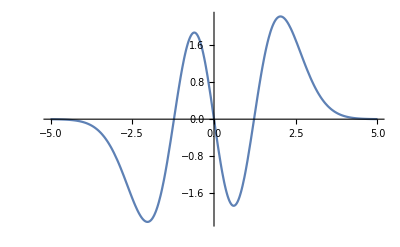

```mathematica
Plot[Evaluate@hoWfnAnalytic[3, y], {y, -5,5}]
```

```mathematica
hoWfnAnalytic[n_, x_]:=1/(√(n!))HermiteH[n, x]*Exp[-x^2/2]
```

```mathematica
bigggo[n_]:=Sum[
hoWfns[[n, i+1]]*
hoWfnAnalytic[i, y], 

{i, 0, Length@hoWfns[[1]]-1}
];
```

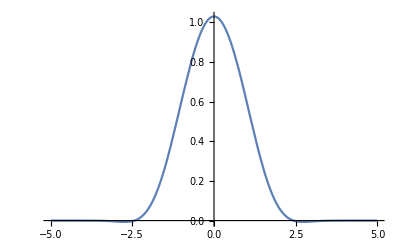

```mathematica
Plot[Evaluate@bigggo[1], {y, -5,5}]
```

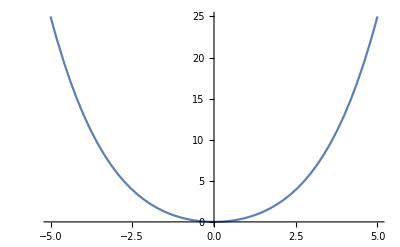

```mathematica
Plot[1/2 x^2+(x^4)/50, {x, -5, 5}]
```

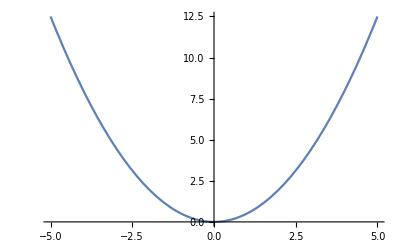

```mathematica
Plot[1/2 x^2, {x, -5, 5}]
```

```mathematica
<<ChemTools`DVR`
```

```mathematica
cdo=ChemDVRObject["Cartesian1DDVR"]
```

ChemDVRObject[…]

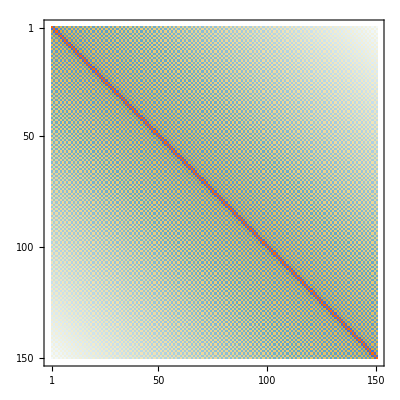

```mathematica
cdo["KineticEnergy", "Points"->{150}]//MatrixPlot
```

```mathematica
cdo["KineticEnergy", "Points"->{150}]+
```

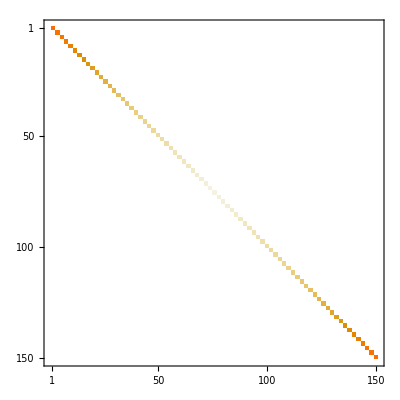

```mathematica
cdo["PotentialEnergy", 
"Points"->{150},
"PotentialFunction"->(#^2 + #^4/50&)
]//MatrixPlot
```

```mathematica
woopy=cdo[ 
"Points"->{500},
"Range"->{-5, 5},
"PotentialFunction"->(#^2 -(#^4)/50&)
]
```

```mathematica
woopy["Wavefunctions"][[;;4]]@"Plot"[]
```